Number of Functions of Finite Sets onto Themselves

Repeated iteration yields at least one fixed point or limit cycle.

http://oeis.org/A001372 - Number of mappings (or mapping patterns) from n points to themselves; number of endofunctions.
http://oeis.org/A000312 - a(n) = n^n; number of labeled mappings from n points to themselves (endofunctions). 

https://oeis.org/A002861 - Number of connected functions (or mapping patterns) on n unlabeled points, or number of rings and branches with n edges.
http://oeis.org/A305754 - Inverse Euler transform of n^n. 
(the labeled version of the previous sequence)

http://oeis.org/A000081 - Number of unlabeled rooted trees with n nodes (or connected functions with a fixed point).
http://oeis.org/A000169 - Number of labeled rooted trees with n nodes: n^(n-1).

https://oeis.org/A000041 - (n) is the number of partitions of n (the partition numbers)
This is the number of divisions of a unary function by its limit cycles (fixed point = length-1 limit cycle).
It can be calculated with the Mathematica function PartitionsP, and also with the Euler partition transform of 1,1,1,1,1,...

For the asymptotic behavior of the number of rooted trees:
http://oeis.org/A051491 - Decimal expansion of Otter’s rooted tree constant: lim_{n->inf} A000081(n+1)/A000081(n).
http://oeis.org/A187770 - Decimal expansion of Otter’s asymptotic constant beta for the number of rooted trees.
http://oeis.org/A086308 - Decimal expansion of Otter’s asymptotic constant beta for the number of unrooted trees.

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Partition Transform.nb"];
```

## Data

```mathematica
(* Zero-based: *)
```

```mathematica
numdata["una"] = {1,1,3,7,19,47,130,343,951,2615,7318,20491,57903,163898,466199,1328993,3799624,10884049,31241170,89814958,258604642,745568756,2152118306,6218869389,17988233052,52078309200,150899223268,437571896993,1269755237948,3687025544605,10712682919341,31143566495273,90587953109272,263627037547365}; (* All unary functions *)
```

```mathematica
numdata["una lbl"] = {1,1,4,27,256,3125,46656,823543,16777216,387420489,10000000000,285311670611,8916100448256,302875106592253,11112006825558016,437893890380859375,18446744073709551616,827240261886336764177,39346408075296537575424,1978419655660313589123979}; (* All labeled unary functions *)
```

```mathematica
numdata["una ird"] = {1,1,2,4,9,20,51,125,329,862,2311,6217,16949,46350,127714,353272,981753,2737539,7659789,21492286,60466130,170510030,481867683,1364424829,3870373826,10996890237,31293083540,89173833915,254445242754,726907585652,2079012341822} ;(* All irreducible (indecomposable) unary functions *)
```

```mathematica
numdata["una ird lbl"] = {1,1,3,23,223,2800,42576,763220,15734388,366715248,9533817400,273549419552,8586984241870,292755986184548,10772849583399474,425587711650564816,17966217346985801150,807152054953801845760,38451365602113352159320,1936082850634342992601636}; (* All labeled irreducible (indecomposable) unary functions *)
```

```mathematica
numdata["una rtt"] = {0,1,1,2,4,9,20,48,115,286,719,1842,4766,12486,32973,87811,235381,634847,1721159,4688676,12826228,35221832,97055181,268282855,743724984,2067174645,5759636510,16083734329,45007066269,126186554308,354426847597,997171512998}; (* All unrooted trees: all unary functions with one fixed point *)
```

```mathematica
numdata["una rtt lbl"] = {0,1,2,9,64,625,7776,117649,2097152,43046721,1000000000,25937424601,743008370688,23298085122481,793714773254144,29192926025390625,1152921504606846976,48661191875666868481,2185911559738696531968,104127350297911241532841,5242880000000000000000000}; (* All labeled unrooted trees: all labeled unary functions with one fixed point *)
```

## Formulas

```mathematica
SetAttributes[numval,Listable]
```

```mathematica
isposint[n_] := If[Head[n]===Integer,n>0,False]
```

```mathematica
ispzint[n_] := If[Head[n]===Integer,n≥0,False]
```

```mathematica
(* All labeled unary functions *)
```

```mathematica
numval["una lbl",n_?ispzint] := If[n>0,n^n,1]
```

```mathematica
(* All labeled unrooted trees: all labeled unary functions with one fixed point *)
```

```mathematica
numval["una rtt lbl",n_?ispzint] := If[n>0,n^(n-1),0]
```

```mathematica
(* All unary functions *)
```

```mathematica
numlistval["una",nmax_?ispzint] := Module[{nroot,afn,x,gen},
nroot = numlistval["una rtt",nmax];
afn[t_] := nroot.t^Range[0,nmax];
gen = 1/Product[1-afn[x^n],{n,nmax}];
CoefficientList[Series[gen,{x,0,nmax}],x]
]
```

```mathematica
(* All irreducible (indecomposable) unary functions to within isomorphism *)
```

```mathematica
numlistval["una ird",nmax_?ispzint] := Module[{nroot,arf,gen,x},
nroot = numlistval["una rtt",nmax];
arf[t_] := nroot.t^Range[0,Length[nroot]-1];
gen = Sum[EulerPhi[j]/j*Log[1/(1-arf[x^j])],{j,nmax}];
CoefficientList[Series[gen+1,{x,0,nmax}],x]
]
```

```mathematica
(* From partition-transform notebook, with zero index added on: *)
```

```mathematica
PartIrredZeroArray[nums_] := Prepend[PartIrredArray[Rest[nums]],First[nums]]
```

```mathematica
PartCompZeroArray[nums_] := Prepend[PartCompArray[Rest[nums]],First[nums]]
```

```mathematica
(* All labeled irreducible (indecomposable) unary functions *)
```

```mathematica
numlistval["una ird lbl",nmax_?ispzint] := PartIrredZeroArray[numval["una lbl",Range[0,nmax]]]
```

```mathematica
(* All unrooted trees: all unary functions with one fixed point *)
```

```mathematica
numlistval["una rtt",nmax_?ispzint] := Module[{a},
a[n_]:=a[n]=If[n≤1,n,Sum[DivisorSum[j,#*a[#]&]*a[n-j],{j,1,n-1}]/(n-1)];
Array[a,nmax+1,0]
]
```

## Tests

```mathematica
numtest[lbl_,serbase_] := (# - Table[numval[lbl,n-1+serbase],{n,Length[#]}])& @ numdata[lbl]
```

```mathematica
numtest[lbl_,serbase_,numterms_] := (# - Table[numval[lbl,n-1+serbase],{n,Length[#]}])& @ Take[numdata[lbl],numterms]
```

```mathematica
numlisttest[lbl_,serbase_] := (# - numlistval[lbl,Length[#]-1+serbase])& @ numdata[lbl]
```

```mathematica
numlisttest[lbl_,serbase_,numterms_] := (# - numlistval[lbl,Length[#]-1+serbase])& @ Take[numdata[lbl],numterms]
```

```mathematica
numlisttest["una",0] // Tally
```

{{0,34}}

```mathematica
numtest["una lbl",0] // Tally
```

{{0,20}}

```mathematica
numlisttest["una ird",0] // Tally
```

{{0,31}}

```mathematica
numlisttest["una ird lbl",0] // Tally
```

{{0,20}}

```mathematica
numlisttest["una rtt",0] // Tally
```

{{0,32}}

```mathematica
numtest["una rtt lbl",0] // Tally
```

{{0,21}}

```mathematica
(* Number of partitions -- limit cycles of a unary function *)
```

```mathematica
numpartitions = {1,1,2,3,5,7,11,15,22,30,42,56,77,101,135,176,231,297,385,490,627,792,1002,1255,1575,1958,2436,3010,3718,4565,5604,6842,8349,10143,12310,14883,17977,21637,26015,31185,37338,44583,53174,63261,75175,89134,105558,124754,147273,173525};
```

```mathematica
numpartitions - PartitionsP[Range[50]-1] // Tally
```

{{0,50}}

```mathematica
numpartitions - PartCompZeroArray[ConstantArray[1,50]] // Tally
```

{{0,50}}

## Display

```mathematica
makepts[data_,serbase_:1] := Transpose[{Range[Length[data]]+1-serbase,data}]
```

```mathematica
shownumdata[lbls_,serbase_:1] := ListLogPlot[makepts[numdata[#],serbase]& /@ lbls,Joined->True,PlotRange->All,PlotLegends->lbls]
```

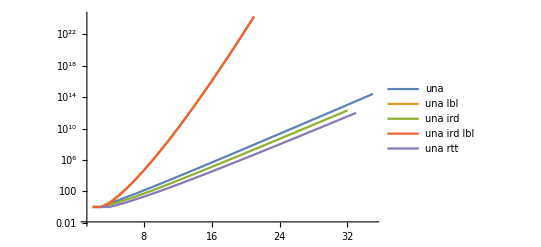

```mathematica
shownumdata[{"una","una lbl","una ird","una ird lbl","una rtt"},0]
```

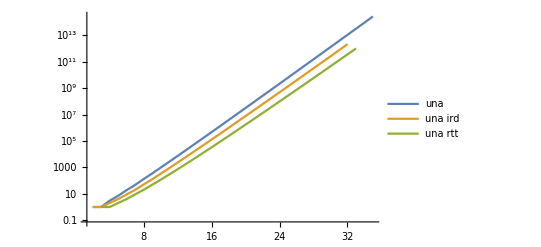

```mathematica
shownumdata[{"una","una ird","una rtt"},0]
```

## Asymptotic behavior

```mathematica
(* OEIS: maxser = 250, digits = 91 (chopped off at 86) *)
```

```mathematica
ottertreecalc[maxser_,digits_:MachinePrecision] := Module[{s,a,A,APrime,eq,c,alpha,b,beta},
s[n_,k_]:=s[n,k]=a[n+1-k]+If[n<2*k,0,s[n-k,k]];a[1]=1;a[n_]:=a[n]=Sum[a[k]*s[n-1,k]*k,{k,1,n-1}]/(n-1);A[x_]:=Sum[a[k]*x^k,{k,0,maxser}];APrime[x_]:=Sum[k*a[k]*x^(k-1),{k,0,maxser}];eq=Log[c]==1+Sum[A[c^-k]/k,{k,2,maxser}];alpha=c/. FindRoot[eq,{c,3},WorkingPrecision->digits];b=Sqrt[(1+Sum[APrime[alpha^-k]/alpha^k,{k,2,maxser}])/(2*Pi)];beta=2*Pi*b^3;<|"Alpha"->alpha,"BetaRoot"->b,"BetaUnrt"->beta|>]
```

```mathematica
otterconst = ottertreecalc[100,16]
```

<|Alpha→2.955765285651994,BetaRoot→0.4399240125710253,BetaUnrt→0.5349496061423072|>

```mathematica
SetAttributes[numasymp,Listable]
```

```mathematica
numasymp["una rtt",n_?ispzint] := If[n>0,otterconst["BetaRoot"] * otterconst["Alpha"]^n * n^(-1.5),0]
```

```mathematica
numasymptest["una rtt",nmax_?ispzint] := Rest[numlistval["una rtt",nmax]]/numasymp["una rtt",Range[nmax]]
```

```mathematica
numasymptest["una rtt",100]
```

{0.769046,0.735915,0.914796,0.952999,1.01384,1.00198,1.02523,1.0153,1.01935,1.01543,1.01539,1.01277,1.01217,1.01063,1.00985,1.00892,1.00827,1.00761,1.0071,1.00662,1.00622,1.00586,1.00554,1.00525,1.00499,1.00475,1.00454,1.00434,1.00416,1.004,1.00384,1.0037,1.00357,1.00345,1.00333,1.00323,1.00313,1.00303,1.00294,1.00286,1.00278,1.00271,1.00264,1.00257,1.0025,1.00244,1.00239,1.00233,1.00228,1.00223,1.00218,1.00213,1.00209,1.00205,1.00201,1.00197,1.00193,1.00189,1.00186,1.00182,1.00179,1.00176,1.00173,1.0017,1.00167,1.00164,1.00162,1.00159,1.00157,1.00154,1.00152,1.0015,1.00148,1.00145,1.00143,1.00141,1.00139,1.00137,1.00136,1.00134,1.00132,1.0013,1.00129,1.00127,1.00125,1.00124,1.00122,1.00121,1.00119,1.00118,1.00117,1.00115,1.00114,1.00113,1.00112,1.0011,1.00109,1.00108,1.00107,1.00106}

```mathematica
numasymptest["una ird/rtt",nmax_?ispzint] := Rest[numlistval["una ird",nmax]]/N[Rest[numlistval["una rtt",nmax]]]
```

```mathematica
numasymptest["una ./rtt",nmax_?ispzint] := Rest[numlistval["una",nmax]]/N[Rest[numlistval["una rtt",nmax]]]/Range[nmax]
```

```mathematica
numasymptest["una ./rtt",30]
```

{1.,1.5,1.16667,1.1875,1.04444,1.08333,1.02083,1.0337,1.01593,1.0178,1.0113,1.01243,1.00973,1.00992,1.00898,1.0089,1.00849,1.0084,1.0082,1.00811,1.00799,1.00792,1.00784,1.00778,1.00772,1.00767,1.00762,1.00758,1.00755,1.00751}

```mathematica
numasymptest["una ird/rtt",nmax_?ispzint] := Rest[numlistval["una ird",nmax]]/N[Rest[numlistval["una rtt",nmax]]]
```

```mathematica
numasymptest["una ird/rtt",30]
```

{1.,2.,2.,2.25,2.22222,2.55,2.60417,2.86087,3.01399,3.21419,3.37514,3.55623,3.71216,3.87329,4.0231,4.17091,4.31212,4.45037,4.58387,4.71426,4.84103,4.96488,5.08577,5.20404,5.31977,5.43317,5.54435,5.65345,5.76058,5.86584}

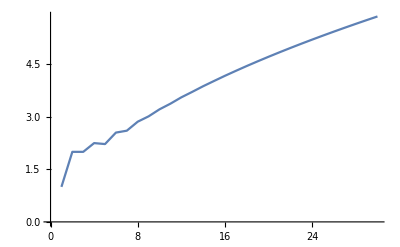

```mathematica
ListPlot[%,Joined->True]
```